```mathematica
SetDirectory[NotebookDirectory[]];
```

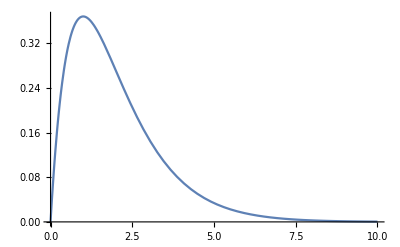

```mathematica
Plot[PDF[GammaDistribution[2,1],x],{x,0,10},PlotRange->Full]
```

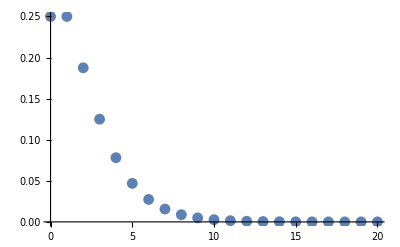

```mathematica
ListPlot[Thread[{Range[21]-1,Table[Assuming[x>0,Integrate[PDF[GammaDistribution[2,1],λ]*PDF[PoissonDistribution[λ],x],{λ,0,∞}]]/.{x->i},{i,0,20}]}]]
```

```mathematica
NIntegrate[PDF[GammaDistribution[2,1],λ]*Likelihood[PoissonDistribution[λ],{2,1,0,5,2,1,1,7,3,2}],{λ,0,∞}]
```

4.48315×10^-10